```mathematica
NotebookEvaluate[NotebookDirectory[]<>"/split_step.nb"];
```

GPE solver v1.4, RZ 2019

```mathematica
dim=1;
NoPotential[];
sizes={256};
timeStep=0.001;
k=-0.5;
contactInteractionFactor=4 Pi k;
initialize[];
gridReport
```

sizes | dim | len | max | min | delta | deltak | maxk
{256} | 1 | 256 | {5} | {-5} | {2/51} | {(51 π)/256} | {(51 π)/2}

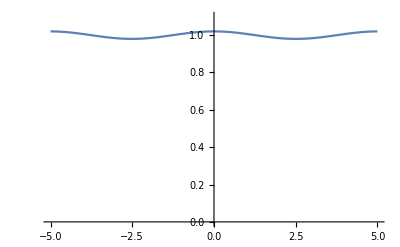

```mathematica
k0=0;
L=max[[1]]-min[[1]]+delta[[1]];
Δk=(2Pi/L)2;
a=0.01;
(* Initial WF: very small modulation with wavenumber Δk *)
psi0[{x_}]:=Exp[I k0 x](1+a Exp[I Δk x]+a Exp[-I Δk x]);
Plot[Abs[psi0[{x}]],{x,min[[1]],max[[1]]},PlotRange->{0,1.1}]
wf=Map[psi0,mesh[],{dim}];
wf/=Sqrt[norm];
```

```mathematica
calcAllTable
p1=plotProjections;
```

time | energies | moments | misc
(0) | (total | -0.313026
kinetic | 0.000156651
potential | 0
contact | -0.313182
virial | -0.312869) | (meanX | 0
sigmaX | 2.90685
norm | 1.) | (steps | 0
A0 | 0.32189)

```mathematica
AbsoluteTiming[evolve["ite",50 ,10]]
```

{5.05085,Null}

time | energies | moments | misc
(50.) | (total | -0.415064
kinetic | 0.382762
potential | 0
contact | -0.797826
virial | -0.0323025) | (meanX | 0
sigmaX | 3.26555
norm | 1.) | (steps | 50000
A0 | 0.619035)

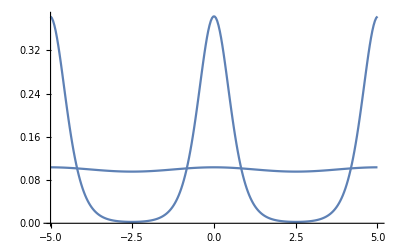

```mathematica
calcAllTable
p2=plotProjections;
Show[p1,p2,PlotRange->All,AxesOrigin->{-5,0}]
```

```mathematica
reportEnergies
```

time | total | kinetic | potential | contact | virial
0 | -0.313026 | 0.000156651 | 0 | -0.313182 | -0.312869
5. | -0.32226 | 0.0160757 | 0 | -0.338336 | -0.306185
10. | -0.411885 | 0.310675 | 0 | -0.72256 | -0.10121
15. | -0.415062 | 0.381649 | 0 | -0.796711 | -0.0334132
20. | -0.415064 | 0.382747 | 0 | -0.797812 | -0.0323168
25. | -0.415064 | 0.382762 | 0 | -0.797826 | -0.0323026
30. | -0.415064 | 0.382762 | 0 | -0.797826 | -0.0323025
35. | -0.415064 | 0.382762 | 0 | -0.797826 | -0.0323025
40. | -0.415064 | 0.382762 | 0 | -0.797826 | -0.0323025
45. | -0.415064 | 0.382762 | 0 | -0.797826 | -0.0323025
50. | -0.415064 | 0.382762 | 0 | -0.797826 | -0.0323025

```mathematica
reportMoments
```

time | meanX | sigmaX | norm
0 | 0 | 2.90685 | 1.
5. | 0 | 2.98749 | 1.
10. | 0 | 3.24033 | 1.
15. | 0 | 3.2652 | 1.
20. | 0 | 3.26555 | 1.
25. | 0 | 3.26555 | 1.
30. | 0 | 3.26555 | 1.
35. | 0 | 3.26555 | 1.
40. | 0 | 3.26555 | 1.
45. | 0 | 3.26555 | 1.
50. | 0 | 3.26555 | 1.

```mathematica
reportMisc
```

time | steps | A0
0 | 0 | 0.32189
5. | 5000 | 0.38031
10. | 10000 | 0.592161
15. | 15000 | 0.618649
20. | 20000 | 0.61903
25. | 25000 | 0.619034
30. | 30000 | 0.619035
35. | 35000 | 0.619035
40. | 40000 | 0.619035
45. | 45000 | 0.619035
50. | 50000 | 0.619035